# [WWS21] Searching for rules that generate elementary particle behavior in the Wolfram Model

Paul Fischer

Goals of the Project: Topological obstructions in a hypergraph that are locally stable under the application of rules are candidates for elementary particles in the Wolfram Model. In this project, we create a hypergraph from a planar, triangular tiling, insert a nonplanar hypergraph (K_5 or K_(3,3)) as an obstruction, and search for rules in which the obstruction’s effects stay localized using a high-level machine learning-based clustering analysis method. The goal of the project is to create conditions that exhibit behavior in the Wolfram Model analogous to the motion of an elementary particle moving through spacetime. 
Main Result: N/A
Future Work: In this project, nonplanar structures were used as the topological obstructions, spacetime was modeled as a planar, triangular tiling, and only one obstruction was placed in the hypergraph. Other types of discrete spacetime meshes and obstructions should be explored, as well as the effects on the multiway graphs associated with these simulations.  Once a solid framework has been set up for the classification of individual elementary particles, multiple particles could be added to the system to explore analogies to quantum statistics or the dynamics of virtual particles in the quantum foam.

## I. Introduction

A unifying theory of quantum mechanics and general relativity has remained elusive for theoretical physicists who have been especially frustrated by this problem since the mid-20th century when the Standard Model was created to model electromagnetic and nuclear interactions via a quantum field theory. The Wolfram Model provides a unique perspective on the generation of spacetime, one which may provide the discrete features required by quantum mechanics while also adhering to the curvilinear features required by general relativity [1]. In the Wolfram Model, a discrete spacetime mesh is modeled by a hypergraph that evolves under the application of rules like a cellular automaton. In order to connect this model to existing theories in physics, there needs to be an established framework for generating behavior analogous to that of elementary particles moving through spacetime.
	
	There are only two nonplanar structures whose variations create local nonplanarity in graphs: K_5 and K_(3,3). We will insert these structures into a planar graph as perturbations and use rules that preserve planarity with the hope that the evolution of this hypergraph will display a protected topological obstruction that behaves like a particle (not spontaneously annihilated) as it moves throughout spacetime. We will use a planar, triangular tiling for our spacetime mesh and search for rules that will only make localized changes in this hypergraph. The high-level machine-learning based clustering analysis method FindClusters built into the Wolfram Language will be used to search for a cluster of rules that generate localized changes in the perturbed space’s evolution.
	
	The structure of this project notebook is as follows: in section II, we will create the discrete spacetime mesh we will be using in this project. In section III, we will insert as a perturbation the nonplanar graph K_5 into the spacetime mesh. In section IV, we will detail the methods and tools we will use to determine which rules create particle-like behavior given our initial conditions. In section V, we will acquire and analyze the dataset gathered for our different evolutions and draw from them the rules that will let us get what we’re going for.

## II. Creating the discrete spacetime mesh

We begin our search by generating the spacetime mesh that we will be using. Below, we generate a 10x10 vertex hypergraph comprised of a planar, triangular tiling (we will be generating a larger hypergraph later when we are looking for elementary particles).

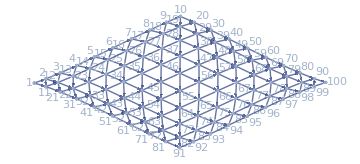

```mathematica
unpertHypergraph=tileTriHGraph[10,10];
[unpertHypergraph,VertexLabels->Automatic,ImageSize->Medium]
```

The next step is to insert a nonplanar hypergraph as a perturbation which is analogous to inserting a particle into the discrete spacetime mesh we just generated.

## III. Inserting K_5 into the the spacetime mesh

There are two nonplanar graphs whose variations generate all possible nonplanar subgraphs in a hypergraph: K_5 and K_(3,3). We will begin by focusing on K_5, which we can see represented as a hypergraph below.

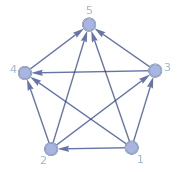

```mathematica
k5={{1,2},{1,3},{1,4},{1,5},{2,3},{2,4},{2,5},{3,4},{3,5},{4,5}};
[k5,VertexLabels->Automatic,ImageSize->Small]
```

Now, we insert the K_5 hypergraph above into the spacetime we generated previously.

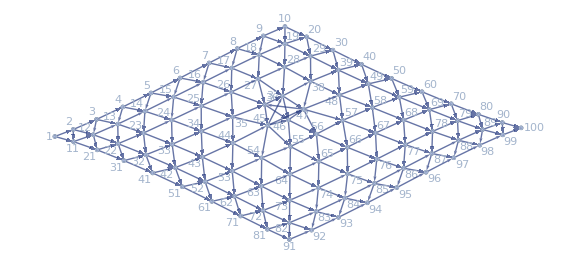

```mathematica
pertHypergraph=pertK5[unpertHypergraph];
[pertHypergraph,VertexLabels->Automatic,ImageSize->Large]
```

Now that we have inserted a particle into our spacetime mesh, we can create the tools to search for rules that lead to elementary particle-like behavior.

## IV. Creating the tools to search for rules with particle-like behavior

Our goal is to find the rules that result in localized changes in the evolution of the perturbed hypergraph. The rules need to have specific properties: we want to be able to specify some range of vertices and generate all of the rules that preserve both the planarity and the number of edges of the associated connected graphs (NOTE: rules that only change the direction of the hypergraphs seemed to yield similar hypergraph evolutions, so they will not be included in this list. However, the differences in their causal graphs were non trivial so they may be worth investigating). Let us view, for example, all of the connected, planar graphs with 4 vertices and 4 edges in randomized directions below.

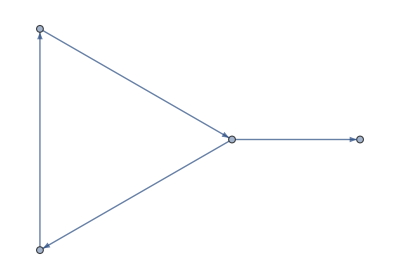
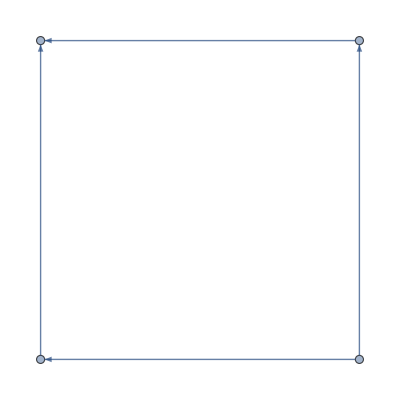

```mathematica
fourVtx4Edge=dirConnPlanarGraphs[4,4]
```

We need to convert these directed graphs into lists that can be turned into hypergraphs by a Wolfram Model Resource Function. We can demonstrate this with the first directed graph above.

```mathematica
fmtdFourVtx4Edge=fmtDirGraph[fourVtx4Edge[[1]]]
```

{{2,1},{1,3},{3,2},{3,4}}

Now we want to generate all of the rules that can be made out of the permutations of the graphs in the above list.

```mathematica
fourVtx4EdgeRules=genAllRules[4,4]
```

{{{{x,y},{x,z},{y,z},{w,z}}→{{x,y},{w,x},{y,z},{w,z}}},{{{x,y},{w,x},{y,z},{w,z}}→{{x,y},{x,z},{y,z},{w,z}}}}

Now we want to turn all of these rules into the data that is necessary to draw conclusions about whether or not the rule creates a particle. We want to see the rule, a plot of the rule (to make it more human-readable), as well as a plot that highlights the difference in the evolution of the perturbed and unperturbed hypergraphs (for a particle we want to see these changes be localized), and a plot that highlights the differences in the causal graphs between the perturbed and unperturbed hypergraphs with the given rule (this should give us the world line of our particle), and the number of steps of evolution of the unperturbed hypergraph (to see if the rule caused a quick termination). Let us see for example what the data we want to see for the first rule we generated above looks like below for 10 steps of evolution.

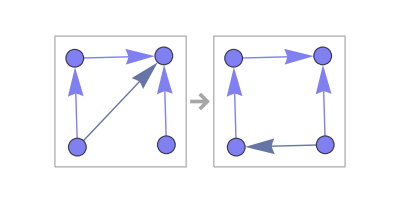
{{{{x,y},{x,z},{y,z},{w,z}}→{{x,y},{w,x},{y,z},{w,z}}},-Graphics-,-Graphics-,-Graphics-,8}

```mathematica
pertGraphData[fourVtx4EdgeRules[[1]],pertHypergraph,unpertHypergraph,10]
```

The function below will give us all of the rules for all permutations from a minimum number of vertices to a maximum number.  Below you can see it for just 4 vertices but with different edge numbers.

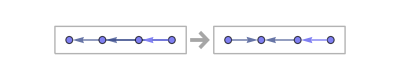
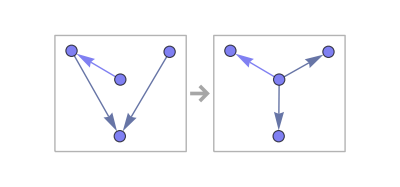
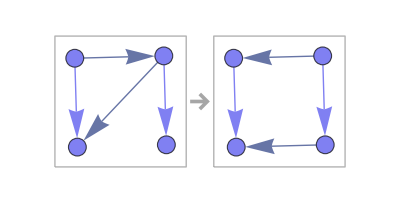
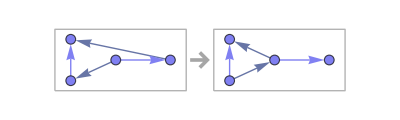
({{{w,x},{w,y},{w,z}}→{{x,y},{z,y},{w,z}}} | -Graphics-
{{{x,y},{z,y},{w,z}}→{{w,x},{w,y},{w,z}}} | -Graphics-
{{{y,x},{z,x},{y,z},{z,w}}→{{y,x},{w,x},{z,y},{z,w}}} | -Graphics-
{{{y,x},{w,x},{z,y},{z,w}}→{{y,x},{z,x},{y,z},{z,w}}} | -Graphics-)

```mathematica
planarityPrsvngRules[4,4]//MatrixForm
```

Now we can generate a dataset of this information for all of the different graphs with different numbers of vertices. We can export the file since it may get large and save it and call on it later.

```mathematica
ptclDatasetExp=ptclEvolData[4,4,pertHypergraph,unpertHypergraph,10];
```

```mathematica
(* please enter the path where you want to save the file here *)
Export["/Users/paulfischer/Desktop/Wolfram\ Winter\ Physics\ School\ 2021/ptclDatasetDemo.wl",ptclDatasetExp];
```

We can get a sense of what the dataset looks like below.

```mathematica
ptclDataset=Import["/Users/paulfischer/Desktop/Wolfram\ Winter\ Physics\ School\ 2021/ptclDatasetDemo.wl"];
```

```mathematica
ptclDataset[[1;;2]]
```

Dataset[<>]

Now that we have collected a small sample data, let’s use the Wolfram Language’s high-level machine learning based clustering analysis method FindClusters to see if we can cluster data by its index in the dataset to see if we can draw rules for any that cluster together looking like particles.

```mathematica
assoc=AssociationThread[Range[Length[ptclDataset]]->Normal[ptclDataset[All,"finalStateHighlight"]]]
```

<|1→-Graphics-,2→-Graphics-,3→-Graphics-,4→-Graphics-|>

```mathematica
FindClusters[assoc]
```

{{1},{2},{3},{4}}

We are looking for localized changes, so the third rule from this dataset looks the most like a particle. Now that we have seen how the data gets created and analyzed with a demonstration, let’s look for some particles!

## V. Acquire and analyze the K_5 perturbation data

We will use the same process as before, but generating a larger hypergraph, in this case 100x100.

```mathematica
unpertHypergraphLargeK5=tileTriHGraph[100,100];
```

Now we insert the perturbation into our mesh.

```mathematica
pertHypergraphLargeK5=pertK5[unpertHypergraphLargeK5];
```

Now we can generate the dataset and save it to a file. In this case, we will search from 4 to 6 vertices for up to 100 evolutions.

```mathematica
ptclDatasetExp=ptclEvolData[4,6,pertHypergraph,unpertHypergraph,100];
```

## Observe the evolution of the K_5 particle in the spacetime mesh

Now, we can apply the planarity-preserving rule triangle-to-line to our particle in spacetime and observe the evolution of the system’s hypergraph and causal graph.

{{x,y},{y,z},{x,z}}→{{x,y},{y,z}}

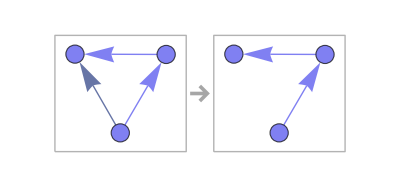

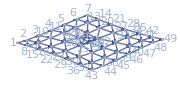

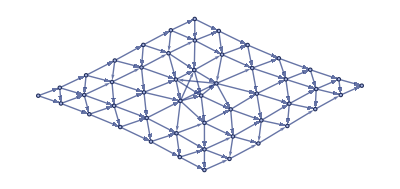
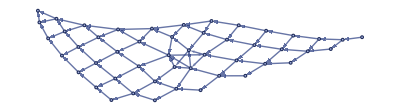
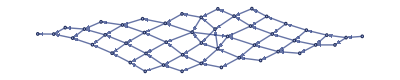
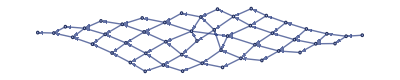

False

-Graphics-

```mathematica
(* create triangle and line for rule triangle-to-line *)
triangle={{1,2},{2,3},{1,3}};
line={{1,2},{2,3}};
(* create the variables for the evolution *)
init=perturbedHGraph;
rule=[triangle->line];
evolObj=[rule,init,10];
dataAssoc=<|"init"->init,"rule"->rule|>;
(* outputs *)
dataAssoc["rule"]
RulePlot[[rule]]
[init,VertexLabels->Automatic,ImageSize->Small]
evolObj["StatesPlotsList"]
PlanarGraphQ[Graph[evolObj["FinalState"]]]
evolObj["CausalGraph"]
```

The localized topological obstruction was preserved during the spacetime mesh’s evolution. However, the evolution terminated quickly and the causal graph turned out to be disconnected. Let us now try this procedure for a larger discrete spacetime mesh and see if the result is any less trivial.

{{x,y},{y,z},{x,z}}→{{x,y},{y,z}}

-Graphics-

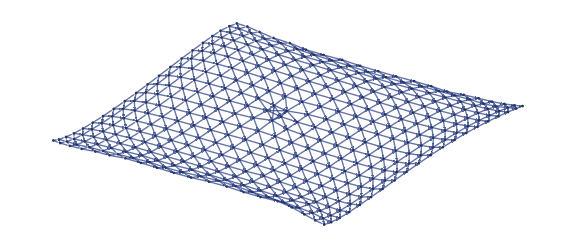
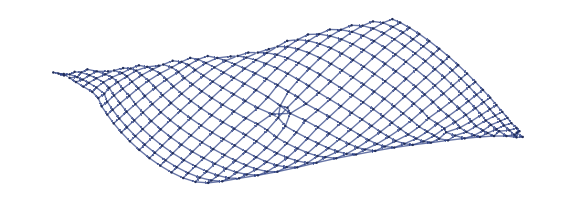
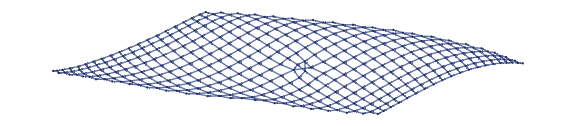
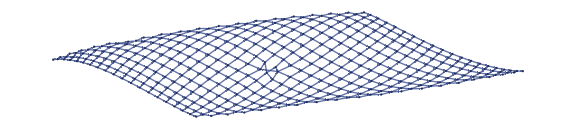

False

-Graphics-

```mathematica
largeHG=tileTriHGraph[20,20];
perturbedHGraph=pertK5[largeHG];
(* create triangle and line for rule triangle-to-line *)
triangle={{1,2},{2,3},{1,3}};
line={{1,2},{2,3}};
(* create the variables for the evolution *)
init=perturbedHGraph;
rule=[triangle->line];
evolObj=[rule,init,100];
dataAssoc=<|"init"->init,"rule"->rule|>;
(* outputs *)
dataAssoc["rule"]
RulePlot[[rule],ImageSize->Tiny]
evolObj["StatesPlotsList",ImageSize->Large]
PlanarGraphQ[Graph[evolObj["FinalState"]]]
evolObj["CausalGraph",ImageSize->Large]
```

Unfortunately, we still see the same trivial behavior.

## Add the particle K_(3,3) to the the spacetime mesh

Let us now test out this procedure with the other nonplanar graph, K_(3,3) (below).

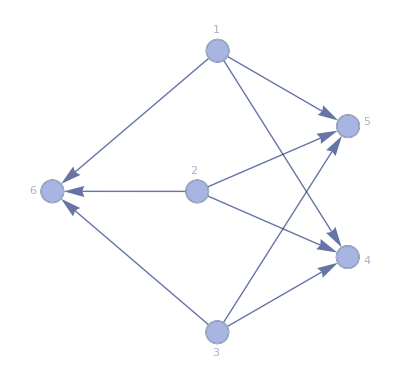

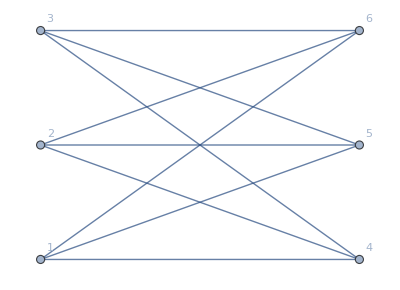

False

```mathematica
k33={{1,4},{1,5},{1,6},{2,4},{2,5},{2,6},{3,4},{3,5},{3,6}};
[k33,VertexLabels->Automatic,ImageSize->Tiny]
Graph[k33,GraphLayout->"MultipartiteEmbedding",VertexLabels->Automatic]
PlanarGraphQ[Graph[k33]]
```

Let us write a function that inserts this graph as a perturbation into the spacetime mesh created above.

```mathematica
pertK33[hypGraph_]:=
(* The function pertk33 adds the nonplanar graph Subscript[K, 3,3] to a triangular,tiled,planar hypergraph created by the function tileTriHGraph. *)
Module[{cols,rows,i,newHypGraph=hypGraph},
(* calculate the # of rows and columns in the inputted hypergraph *)
cols=newHypGraph[[2,2]]-1;
rows=Max[newHypGraph]/cols;
(* calculate the index of the vertex "i" in the middle of the hypergraph of which to add three edges to create Subscript[K, 5]*)
If[OddQ[rows]==True,
i=Floor[Max[newHypGraph]/2],
i=Floor[(Max[newHypGraph]-cols)/2];
];
AppendTo[newHypGraph,{i,i-cols+2}];
AppendTo[newHypGraph,{i+1,i-cols}];
AppendTo[newHypGraph,{i+2,i-cols}];
AppendTo[newHypGraph,{i+2,i-cols+1}];
Return[newHypGraph]
]
```

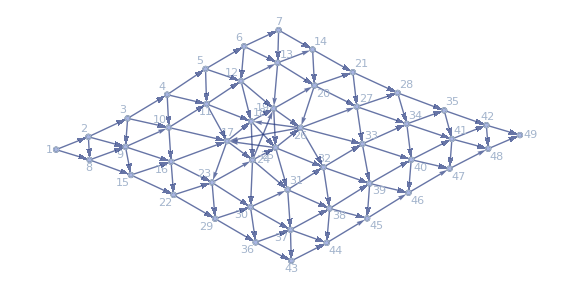

False

```mathematica
k33PerturbedHGraph=pertK33[hG];
[k33PerturbedHGraph,VertexLabels->Automatic,ImageSize->Large]
PlanarGraphQ[Graph[k33PerturbedHGraph]]
```

## Observe the evolution of the K_(3,3) particle in the spacetime mesh

Now we can observe how our spacetime mesh evolves with the K_(3,3) particle in it.

{{x,y},{y,z},{x,z}}→{{x,y},{y,z}}

-Graphics-

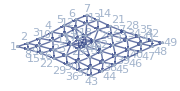

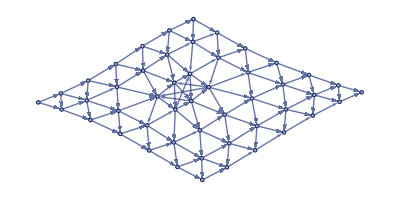
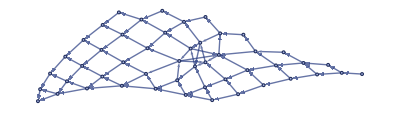
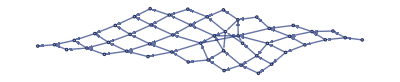
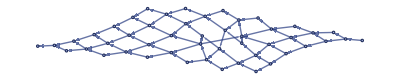

False

-Graphics-

```mathematica
(* create triangle and line for rule triangle-to-line *)
triangle={{1,2},{2,3},{1,3}};
line={{1,2},{2,3}};
(* create the variables for the evolution *)
init=k33PerturbedHGraph;
rule=[triangle->line];
evolObj=[rule,init,10];
dataAssoc=<|"init"->init,"rule"->rule|>;
(* outputs *)
dataAssoc["rule"]
RulePlot[[rule],ImageSize->Tiny]
[init,VertexLabels->Automatic,ImageSize->Small]
evolObj["StatesPlotsList"]
PlanarGraphQ[Graph[evolObj["FinalState"]]]
evolObj["CausalGraph"]
```

We get similar behavior as we did with the last particle. We do not lose the particle from our spacetime mesh (it stays nonplanar), but its evolution still terminated quickly and the causal graph is disconnected. We can again try for a larger spacetime mesh and observe any changes.

{{x,y},{y,z},{x,z}}→{{x,y},{y,z}}

-Graphics-

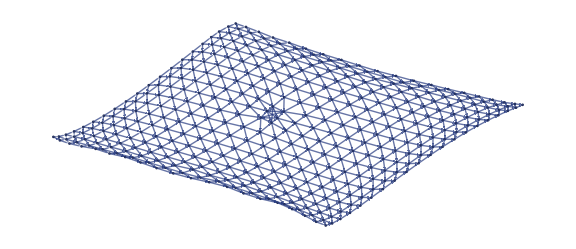
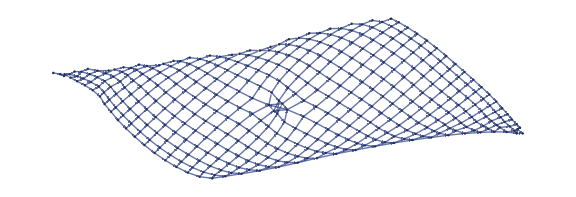
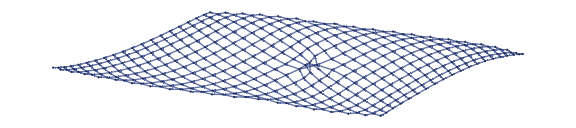
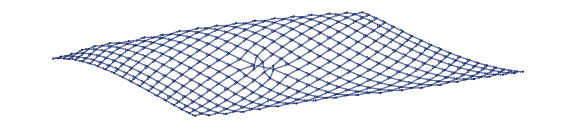

False

-Graphics-

```mathematica
largeK33HG=tileTriHGraph[20,20];
largeK33PerturbedHGraph=pertK33[largeK33HG];
(* create triangle and line for rule triangle-to-line *)
triangle={{1,2},{2,3},{1,3}};
line={{1,2},{2,3}};
(* create the variables for the evolution *)
init=largeK33PerturbedHGraph;
rule=[triangle->line];
evolObj=[rule,init,100];
dataAssoc=<|"init"->init,"rule"->rule|>;
(* outputs *)
dataAssoc["rule"]
RulePlot[[rule],ImageSize->Tiny]
evolObj["StatesPlotsList",ImageSize->Large]
PlanarGraphQ[Graph[evolObj["FinalState"]]]
evolObj["CausalGraph",ImageSize->Large]
```

Unfortunately, we see what we saw before.

## Summary and Conclusions

Unfortunately, this method’s evolution terminates very quickly and creates a disconnected causal graph. Other types of planar hypergraphs and planarity preserving rules should be tested so that any conditions for nontrivial behavior can be discovered. Once a nontrivial motion of a single nonplanar particle has been found, the next step is to observe how the system evolves with the interactions of multiple particles. As more particles are inserted into the system, there may become apparent an analogy to quantum statistics. How these obstructions affect their multiway graphs, as well as the behavior of other types of topological obstructions, should be explored and classified according to data science/machine learning techniques.

## References

[1] Wolfram, Stephen. “A Class of Models with the Potential to Represent Fundamental Physics.” Complex Systems 29.2 (2020): 107–536. Crossref. Web.

## Keywords

Wolfram Model

Topological Obstruction

Machine Learning

Clustering Analysis

## Appendix: Initialization cells with user-defined functions

```mathematica
tileTriHGraph[rows_,cols_]:=
(* The function "tileTriHGraph" creates a triangular, tiled, planar hypergraph with an inputted number of rows and columns. *)
Module[{hypGraph,j,i},
hypGraph={};
(* "j" is the row and "i" is the vertex *)
For[j=1,j≤rows,j++,
(* conditions for each row before the last *)
If[j<rows,
For[i=1+cols*(j-1),i≤cols*j,i++,
(* condition for the first index of the jth row *)
If[i==1+cols*(j-1),
AppendTo[hypGraph,{i,i+1}];
AppendTo[hypGraph,{i,i+cols}]
];
(* condition for the middle indices of the jth row *)
If[i≠1+cols*(j-1)&&i≠cols*j,
AppendTo[hypGraph,{i,i+1}];
AppendTo[hypGraph,{i,i+(cols-1)}];
AppendTo[hypGraph,{i,i+cols}]
];
(* condition for the last index of the jth row *)
If[i==cols*j,
AppendTo[hypGraph,{i,i+(cols-1)}];
AppendTo[hypGraph,{i,i+cols}]
]
],
(* condition for the last row *)
For[i=1+cols*(j-1),i<cols*j,i++,
AppendTo[hypGraph,{i,i+1}]
];
];
];
Return[hypGraph]
]
```

```mathematica
pertK5[hypGraph_]:=
(* The function pertk5 adds the nonplanar graph Subscript[K, 5] as a perturbation to a planar, triangularly tiled hypergraph. 
NOTE: This function is built to to take as input a hypergraph generated by the function tileTriHGraph defined above. *)
Module[{cols,rows,i,newHypGraph=hypGraph},
(* calculate the # of rows and columns of the inputted hypergraph *)
cols=newHypGraph[[2,2]]-1;
rows=Max[newHypGraph]/cols;
(* calculate the index of the vertex "i" in the middle of the hypergraph of which to add three edges to insert Subscript[K, 5] *)
If[OddQ[rows]==True,
i=Floor[Max[newHypGraph]/2],
i=Floor[(Max[newHypGraph]-cols)/2];
];
AppendTo[newHypGraph,{i,i+2}];
AppendTo[newHypGraph,{i,i-cols+2}];
AppendTo[newHypGraph,{i+2,i-cols+1}];
Return[newHypGraph]
]
```

```mathematica
dirConnPlanarGraphs[vtx_,edge_]:=
(* The function dirConnPlanarGraphs returns a list of all of the connected, planar graphs with the inputted number of vertices (vtx) and edges (edge) in randomized directions.
NOTE: The directions are randomized because I was mostly interested in the evolution of the hypergraph which seemed trivially affected by the directions, but the causal graphs seemed to be nontrivially affected by the directions so this function may want to be edited to include all permutations of directions in the future when searching for world lines in causal graphs *)
DirectedGraph[#,"Random"]&/@Select[GraphData/@GraphData["Planar",vtx],ConnectedGraphQ[#]==True&&EdgeCount[#]==edge&]
```

```mathematica
fmtDirGraph[dirGraph_]:=
(* The function fmtDirGraph takes a directed graph as input and returns a formatted list that can be the left or right-hand-side of a Wolfram Model rule. *)
Module[
{i,fmtdList},
fmtdList={};
For[i=1,i≤Length[EdgeList[dirGraph]],i++,
AppendTo[fmtdList,{EdgeList[dirGraph][[i,1]],EdgeList[dirGraph][[i,2]]}]
];
Return[fmtdList]
]
```

```mathematica
genAllRules[vtx_,edge_]:=
(* The function genAllRules returns a list of all of the possible rules (directed graph -> directed graph) for permutations of randomly directed, connected, planar graphs with an inputted number of vertices (vtx) and edges (edge). 
NOTE: This function depends on the user-defined function dirConnPlanarGraphs. *)
Module[
{perm,i,rule},
rule={};
perm=Permutations[dirConnPlanarGraphs[vtx,edge],{2}];
For[i=1,i≤Length[perm],i++,
AppendTo[rule,
{fmtDirGraph[perm[[i,1]]]->fmtDirGraph[perm[[i,2]]]}];
];
Return[/@rule]
]
```

```mathematica
pertGraphData[rule_,pertInit_,unpertInit_,evolSteps_]:=
(* The function pertGraphData takes as input a rule, perturbed and unperturbed hypergraphs, and the number of steps desired in the evolution. It returns a list containing the rule, a plot of the rule, a plot highlighting the difference between the perturbed and unperturbed final state graphs, a plot highlighting the difference between their respective causal graphs, and the number of evolution states of the unperturbed hypergraph. *)
Module[
{pertEvolObj,unpertEvolObj,data,causalGraphDiff},
pertEvolObj=[rule,pertInit,evolSteps];
unpertEvolObj=[rule,unpertInit,evolSteps];
causalGraphDiff=GraphDifference[unpertEvolObj["CausalGraph"],pertEvolObj["CausalGraph"]];
data={
rule,
RulePlot[[rule]],
(* finds the difference between the last evolution step of the perturbed and unperturbed hypergraphs, the perturbed evolution object is truncated in an effort to maintain an equal length between both states lists *)
Last[MapThread[[#,EdgeStyle-><|Alternatives@@#2->Directive[Thick,Red]|>,ImageSize->120]&,{unpertEvolObj["StatesList"],MapThread[Complement,{unpertEvolObj["StatesList"],pertEvolObj["StatesList"][[1;;Length[unpertEvolObj["StatesList"]]]]}]}]],
HighlightGraph[unpertEvolObj["CausalGraph"],causalGraphDiff,GraphHighlightStyle->"Thick"],Length[unpertEvolObj["StatesList"]]};
Return[data]
]
```

```mathematica
planarityPrsvngRules[minVtx_,maxVtx_]:=
(* The function planarityPrsvngRules generates a list of all of the Wolfram Model rules that preserve planarity for a minimum and maximum number of vertices. 
NOTE: This function depends on the user-defined function genAllRules *)
Module[
{i,j,ruleForm,rulePlots,k,rulesList},
rulesList={};
For[i=minVtx,i≤maxVtx,i++,
(* starts looking for rules with iteration vertex - 1 edges and keeps looking for rules with increasingly more edges until it reaches its first edge number that does not have any associated planarity preserving rules *)
j=i-1;
While[genAllRules[i,j]≠{},
ruleForm=genAllRules[i,j];
rulePlots=RulePlot/@/@ruleForm;
For[k=1,k≤Length[ruleForm],k++,
rulesList=AppendTo[rulesList,{ruleForm[[k]],rulePlots[[k]]}]
];
j=j+1
]
];
Return[rulesList]
]
```

```mathematica
ptclEvolData[minVtx_,maxVtx_,pertInit_,unpertInit_,evolSteps_]:=
(* The function ptclEvolData returns a dataset containing the data collected for all of the rules collected for a range of vertices.
NOTE: This function depends on the user-defined functions planarityPrsvngRules and pertGraphData. *)
Module[
{rules,data,dataAssoc,i},
dataAssoc={};
rules=planarityPrsvngRules[minVtx,maxVtx];
For[i=1,i≤Length[rules[[All,1]]],i++,
data=pertGraphData[rules[[i,1]],pertInit,unpertInit,evolSteps];
AppendTo[dataAssoc,<|"rule"->data[[1]],"rulePlot"->data[[2]],"finalStateHighlight"->data[[3]],"causalGraphHighlight"->data[[4]],"states"->data[[5]]|>]
];
Return[Dataset[dataAssoc]]
]
```